#### Initialise RQA

Load Flip Phillips’ RQA package:

```mathematica
Get[FileNameJoin[{ResourceFunction["NotebookRelativePath"][{"..","RQA/RQA"}],"RQAth1.wl"}]]
```

List the functions in the RQA package:

```mathematica
?RQA`*
```

The package is built on the equations expressed in Webber (2012) and in Webber and Marwan (2015).

#### Load data

```mathematica
SetDirectory["C:\\Users\\User\\GitHub\\Project\\Data"]
```

C:\Users\User\GitHub\Project\Data

```mathematica
data=Flatten[ReadList["MagSusAll Decimate"]];
```

```mathematica
Length[data]
```

2191

Issue

Using Drawing Tools and the Get Coordinates Tool-Graphics-I should be able to Use Alt+drag to mark a rectangle. I cannot. I use this Plot[] command as this is a WL example, and I cannot get it to work even within the WL example page howto/GetCoordinatesForPointsInAPlot

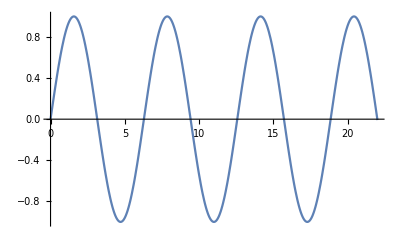

```mathematica
Plot[Sin[x],{x,0,22}]
```

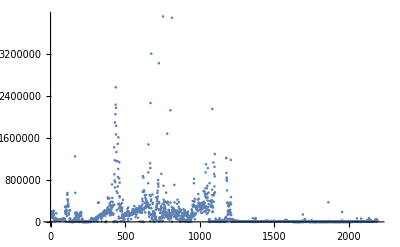

```mathematica
ListPlot[data,PlotRange->All]
```

### Comment

I choose this window based on the pattern of the DistanceMap

```mathematica
amwin=1; anwin=400;
```

```mathematica
awin=data[[amwin;;anwin]];
```

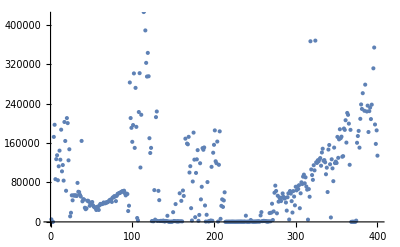

```mathematica
ListPlot[awin]
```

#### Create a time series

Create a time series of the data:

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

```mathematica
dsa=RQAMakeTimeSeries[awin,1,1]
```

TimeSeries[…]

```mathematica
ds["LastTime"];
```

```mathematica
mintimeseries=Min[ds["Values"]];
```

```mathematica
maxtimeseries=Max[ds["Values"]];
```

#### Estimate the lag and embedding dimensions for the data

The lag is first estimated:

```mathematica
lag=RQAEstimateLag[ds]
```

151.

```mathematica
lag=RQAEstimateLag[dsa]
```

24.5243

### Comment

Choose your own lag. I choose 1  so as more directly to be able to compare the maps of the epochs with the original map.

```mathematica
lag=1
```

1

The embedding dimension of the system, that dimension for which the calculated fractal dimension no longer increases, is then estimated:

```mathematica
(*RQAEstimateDimensionality[dsa,lag]*)
```

Construct the embedding, which is now a list of 3 columns of data, offset by the lag:

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

```mathematica
embeddinga=RQAEmbed[dsa,3,lag]
```

TimeSeries[…]

```mathematica
embedvalues=embedding["Values"];
```

```mathematica
embedvaluesa=embeddinga["Values"];
```

Display the embedding:

```mathematica
ListPlot[embedding];
```

#### Plot the 3D spatial attractor

Plot the attractor with axes {t,t+i,t+2i}:   Can’t cope if embedding dimension is greater than 3.

```mathematica
ListPointPlot3D[embedvaluesa,PlotRegion->All,SphericalRegion->True,Boxed->True,AxesLabel->{t, t+5, t+10}];
```

```mathematica
ParametricPlot3D[embeddinga[t],{t,1,2100},PlotRegion->All,SphericalRegion->True,Boxed->True,AxesLabel->{t, t+5, t+10}];
```

```mathematica
junk=BSplineCurve[{embedvalues}];
Tube[junk];
Graphics3D[{Orange,Specularity[White,10],Tube[junk,.002]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Yellow,Bold],AxesLabel->{t, t+5, t+10},ViewPoint->Front,ImagePadding->5];
```

```mathematica
junk=BSplineCurve[{embedvaluesa}];
Tube[junk];
Graphics3D[{Orange,Specularity[White,10],Tube[junk,.002]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Yellow,Bold],AxesLabel->{t, t+5, t+10},ViewPoint->Front,ImagePadding->5];
```

#### Calculate the distance map and the recurrence map

Using estimated values for  lag and for embedding dimension, calculate the distance map:

(*Options[RQADistanceMap]={
   DistanceFunction->SquaredEuclideanDistance,
   “Rescale”->False,”RescaleFunction”->Automatic}
   
RQADistanceMap[ts_,OptionsPattern[]]:=Module[{df,rescale,map,rf},
   df=OptionValue[DistanceFunction];
   rescale=OptionValue[“Rescale”];
   rf=OptionValue[“RescaleFunction”];
   rf=If[rf===Automatic,Rescale,rf];
   
   map=Outer[df,ts[“Values”],ts[“Values”],1];
   If[rescale,rf[map],map]]*)

```mathematica
dm=RQADistanceMap[embedding];
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

```mathematica
(*dm=RQADistanceMap[embedding];
InputForm[MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]]*)
```

```mathematica
(*dm=RQADistanceMap[embedding];
AbsoluteOptions[ArrayPlot[dm,DataReversed->{True,False},PlotRange->Automatic,ColorFunction->Automatic],PlotRange]*)
```

```mathematica
(*FullForm[%]*)
```

```mathematica
PlotRange[%]
```

PlotRange::gtype: Symbol is not a type of graphics.

PlotRange[Null]

### Comment

Just learning. I want to draw my own boxes on top of the distance map - and eventually have this happen automatically.

```mathematica
Graphics[Line[{Scaled[{0,.2}],Scaled[{1,.8}]}],Frame->True,PlotRange->{{0.,1.},{0.,1.}}]
```

-Graphics-

```mathematica
PlotRange[%]
```

{{0.,1.},{0.,1.}}

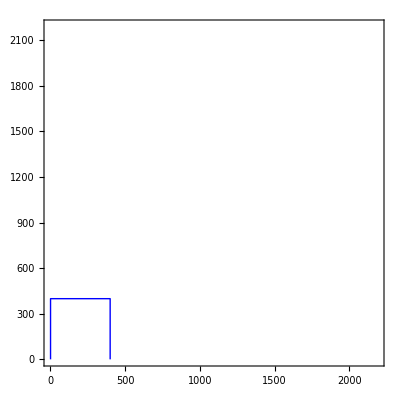

```mathematica
sqwins=Graphics[{Thick,Blue,Line[{{1,1},{1,400},{400,400},{400,1}}]},Frame->True,PlotRange->{{1,2189},{1,2189}}]
```

```mathematica
PlotRange[%]
```

{{1.,2189.},{1.,2189.}}

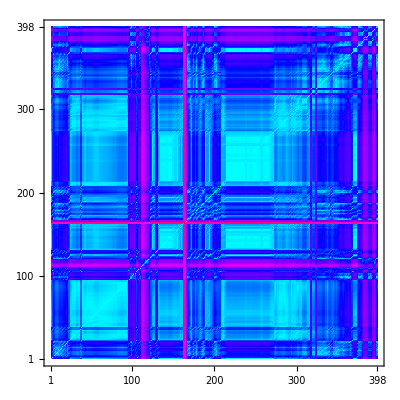

```mathematica
dma=RQADistanceMap[embeddinga];
MatrixPlot[dma,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

```mathematica
PlotRange[%]
```

{{0.,398.},{0.,398.}}

Using estimated values for  lag and for embedding dimension, calculate the recurrence map:

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
rma=RQARecurrenceMap[embeddinga];
```

The recurrence map may be plotted :

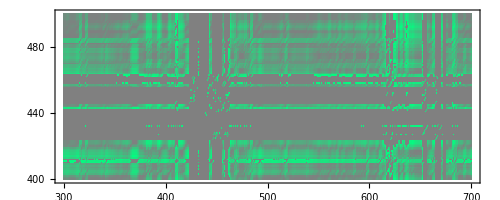

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->{{400,500},{300,700}},ColorFunction->(g↦RGBColor[1-g,g,1/2])]
```

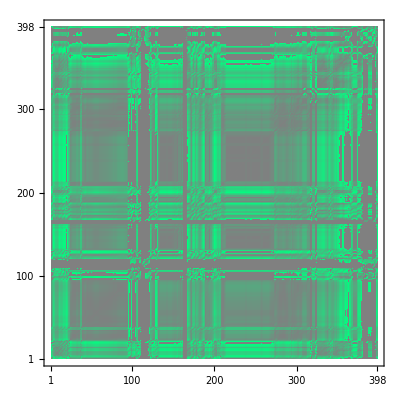

```mathematica
MatrixPlot[rma,DataReversed->{True,False},PlotRange->All,ColorFunction->(g↦RGBColor[1-g,g,1/2])]
```

```mathematica
N[RQARecurrence[rm]]
```

0.866356

```mathematica
N[RQARecurrence[rma]]
```

0.779072

```mathematica
N[RQADeterminism[rm]]
```

0.997905

```mathematica
N[RQADeterminism[rma]]
```

0.995954

### Issue

The following errors are new with version ‘2’ of RQA. I just changed the threshold to 1 (see RQAth1.wl) but it hasn’t made any difference.

```mathematica
N[RQALaminarity[rm]]
```

2.40996×10^-7 RQANVerticalRecurrentPoints[SparseArray[<4149442>, {2189, 2189}],1.]

```mathematica
N[RQALaminarity[rma]]
```

8.12361×10^-6 RQANVerticalRecurrentPoints[SparseArray[<123098>, {398, 398}],1.]

```mathematica
N[RQATrappingTime[rm]]
```

Mean[RQAVerticalLineLengths[SparseArray[<4149442>, {2189, 2189}],1.]]

```mathematica
N[RQATrappingTime[rma]]
```

Mean[RQAVerticalLineLengths[SparseArray[<123098>, {398, 398}],1.]]

```mathematica
N[RQATrend[rm]]
```

RQATrend[SparseArray[<4149442>, {2189, 2189}]]

```mathematica
N[RQATrend[rma]]
```

RQATrend[SparseArray[<123098>, {398, 398}]]

```mathematica
N[RQAEntropy[rm]]
```

Entropy::targ: Argument RQADiagonalLineLengths[«1»,1] at position 2 should be a List, a SparseArray, or a String.

Entropy::targ: Argument RQADiagonalLineLengths[«1»,1.] at position 2 should be a List, a SparseArray, or a String.

Entropy[2.,RQADiagonalLineLengths[SparseArray[<4149442>, {2189, 2189}],1.]]

```mathematica
N[RQAEntropy[rma]]
```

Entropy::targ: Argument RQADiagonalLineLengths[SparseArray[Automatic,«2»,{1,{{0,«398»},{«1»}},{2.97545×10^10,6.84735×10^10,7.42263×10^10,6.05039×10^10,4.10159×10^10,4.02326×10^10,«123086»,1.16149×10^10,1.20712×10^10,1.66723×10^10,5.58248×10^10,3.89907×10^10,4.94475×10^9}}],1] at position 2 should be a List, a SparseArray, or a String.

Entropy::targ: Argument RQADiagonalLineLengths[SparseArray[Automatic,«2»,{1,{{0,«398»},{«1»}},{2.97545×10^10,6.84735×10^10,7.42263×10^10,6.05039×10^10,4.10159×10^10,4.02326×10^10,«123086»,1.16149×10^10,1.20712×10^10,1.66723×10^10,5.58248×10^10,3.89907×10^10,4.94475×10^9}}],«3»] at position 2 should be a List, a SparseArray, or a String.

Entropy[2.,RQADiagonalLineLengths[SparseArray[<123098>, {398, 398}],1.]]

```mathematica
N[RQADmax[rm]]
```

980.

```mathematica
N[RQADmax[rma]]
```

195.

```mathematica
N[RQAVmax[rm]]
```

RQAVerticalLineLengths[SparseArray[<4149442>, {2189, 2189}],1.]

```mathematica
N[RQAVmax[rma]]
```

RQAVerticalLineLengths[SparseArray[<123098>, {398, 398}],1.]

```mathematica
N[RQAChaos[rm]]
```

1/RQADiagonalLineLengths[SparseArray[<4149442>, {2189, 2189}],1.]

```mathematica
N[RQAChaos[rma]]
```

1/RQADiagonalLineLengths[SparseArray[<123098>, {398, 398}],1.]

#### Time Series Epochs start here

The following properties describe the dataset:

```mathematica
ds["Properties"]
```

{DatePath,Dates,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

```mathematica
dsw=TimeSeriesWindow[ds,{1,Length@data}]
```

TimeSeries[…]

### Issue

So why, if I type dsw[100], it gives me the relevant value for the position 100 in the time series, but if I do the same for eps3, see below, it does not work? I am presently exploring TimeSeriesWindow as I think use of this may result in a different format. There are many consequences, one them being that 
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange→All] works but Plot[eps3[t],{t,eps3["FirstTime"],eps3["LastTime"]},PlotRange→All] does not.

```mathematica
Head[dsw]
```

TemporalData

```mathematica
dsw[100]
```

162556.

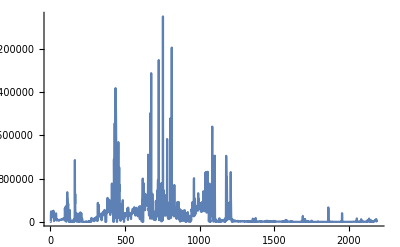

```mathematica
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange->All]
```

```mathematica
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange->All,data];
```

Plot::nonopt: Options expected (instead of data) beyond position 2 in Plot[dsw[t],{t,dsw[FirstTime],dsw[LastTime]},PlotRange→All,data]. An option must be a rule or a list of rules.

Compute the time series epochs for the distance map. In this example, 500 is the size of the moving window, and 250 is the number of steps by which it is moved.

```mathematica
eps=RQATimeSeriesEpochs[dsw,500,250]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

```mathematica
Head[eps]
```

List

```mathematica
eps3=TemporalData[Take[eps,{3}]]
```

TemporalData[…]

```mathematica
eps5=TemporalData[Take[eps,{5}]]
```

TemporalData[…]

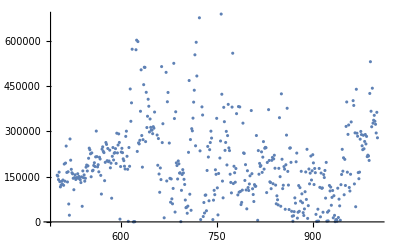

```mathematica
ListPlot[eps3]
```

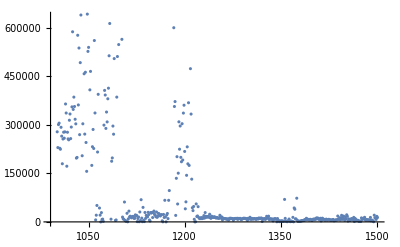

```mathematica
ListPlot[eps5]
```

```mathematica
eps3
```

TemporalData[…]

```mathematica
patheps3=eps3["Path"];
```

```mathematica
patheps5=eps5["Path"];
```

```mathematica
Head[patheps3]
```

List

```mathematica
ListPlot[patheps5]
```

-Graphics-

```mathematica
patheps3[[1]]
```

{501,154594.}

```mathematica
timeeps3=eps3["Times"];
```

```mathematica
timeeps3=eps3["FirstTime"]
```

501

```mathematica
timeeps3[[201]]
```

Part::partd: Part specification 501⟦201⟧ is longer than depth of object.

501⟦201⟧

```mathematica
eps3["Values"];
```

```mathematica
Length[patheps3]
```

501

```mathematica
patheps3[[201]]
```

{701,72421.5}

### Issue

As already commented above, why does this command not work?

```mathematica
Plot[eps3[t],{t,eps3["FirstTime"],eps3["LastTime"]},PlotRange->All]
```

-Graphics-

Estimate the lag for each of the time series:

```mathematica
taus=Quiet@Map[RQAEstimateLag,eps]
```

{7.,68.,183.379,183.379,183.379,183.379,183.379}

Compute the mean of the lags:

```mathematica
Mean[taus]
```

141.699

Compute a list of time series for the epochs for the distance map, each of which it is possible to address and plot separately:

```mathematica
embeds=Map[RQAEmbed[#,3,1.0]&,eps];
```

Compute the distance maps for each epoch:

```mathematica
maps=RQADistanceMap/@embeds;
```

Display the main distance map There appears to be an upper limit to the number of pixels forming a plot - of 570 - is this correct?

```mathematica
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue,Frame->True]
```

-Graphics-

Since the recurrence map is calculated for each epoch, the colour ranges are slightly different from the main distance map. As I’ve done it here, it is easy to match the epoch maps to the main map. I want to label each epoch map though with its correct number - 1-201, 151-351, and so on - and then I want to be able to refer each number to the depth in the drill hole, if at all possible given the lag. So dmeps3 should have axes from 301-501.

```mathematica
eps3["FirstTime"]
```

501

```mathematica
Plot[eps3[t],{t,eps3["FirstTime"],eps3["LastTime"]},PlotRange->All]
```

-Graphics-

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->Automatic,ColorFunction->Hue]&/@maps
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dmeps3=RQADistanceMap[eps3];
MatrixPlot[dmeps3,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue,FrameTicks->{{{1,101,201,301,eps3["FirstTime"],eps3["LastTime"]},None},{None,None}}]
```

-Graphics-

```mathematica
eps5["FirstTime"]
```

1001

```mathematica
eps5["LastTime"]
```

1501

```mathematica
dmeps5=RQADistanceMap[eps5];
MatrixPlot[dmeps5,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue,FrameTicks->{{{1,101,201,301,eps5["FirstTime"],eps5["LastTime"]},None},{None,None}}]
```

-Graphics-

```mathematica
GraphicsGrid@{MatrixPlot[#,DataReversed->{True,False},FrameTicks->Automatic,ColorFunction->Hue]&/@maps};
```

Compute a list of time series for the epochs for the distance map, again, each of which it is possible to address and plot separately:

```mathematica
numbers=RQARecurrenceMap[#]&/@embeds;
```

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->Automatic,ColorFunction->Hue]&/@numbers;
```

```mathematica
GraphicsGrid@{MatrixPlot[#,DataReversed->{True,False},FrameTicks->Automatic,ColorFunction->Hue]&/@numbers};
```

Similarly here for VMAX. The segment lengths are for the verticals.

```mathematica
TabView[{"Rec"->ListLinePlot[N[RQARecurrence/@numbers]],"Det"->ListLinePlot[N[RQADeterminism/@numbers]],"Lam"->ListLinePlot[N[RQALaminarity/@numbers]],"Trap"->ListLinePlot[N[RQATrappingTime/@numbers]],"Trend"->ListLinePlot[N[RQATrend/@numbers]],"Entropy"->ListLinePlot[N[RQAEntropy/@numbers]],"Dmax"->ListLinePlot[N[RQADmax/@numbers]],"Vmax"->ListLinePlot[N[RQAVmax/@numbers]],"Chaos"->ListLinePlot[N[RQAChaos/@numbers]]}]
```

Entropy::targ: Argument RQADiagonalLineLengths[SparseArray[Automatic,«3»],1] at position 2 should be a List, a SparseArray, or a String.

General::stop: Further output of Entropy::targ will be suppressed during this calculation.

123456789

Measures used in recurrence quantification analysis (RQA). 
 Recurrence rate  Recurrent points falling within a given radius for the number of points in signal. 
 Determinism Recurrent points forming diagonal line structures; Predictability of the system 
 Laminarity Recurrent points forming vertical line structures; intermittency of system. 
 Trapping time Average length of vertical line structures. Length of time (or space) system remains in a specific state. 
 Trend A measure of system stationarity. 
 Entropy The Shannon information entropy of probability distribution of the diagonal line lengths. Complexity of deterministic structures. 
 Dmax Length of the longest diagonal line. The shorter the line, the faster the divergence of the phase space trajectory. 
 Vmax Length of the longest vertical line. 
 Chaos 1/Dmax Interpreted to be equivalent to the maximum Lyapunov exponent of the system.

Significance of patterns in recurrence plots

-Graphics-

#### To do notes

8 July 2019
• modify the existing epoch plots so that the x axis represents the absolute position within the timeseries, not just the position within the epoch.
• Work out how to interrogate a particular RQA while moving through the data - 12 little recurrence plots look very pretty - but how about when you interrogate 120,000 points, 260,000 points, 1 trillion points?
•  A related problem - within the recurrence plot for all data (or at least the data you wish to explore), how do you visualise/manipulate a window representing TimeSeriesEpochs moving up and down the line of identity (LOI) of the main distance plot with the distance plot representing the epoch showing up on the side?
•  How do you do all this for 2D? 3D?